### Polynomials

```mathematica
fPol[t_]:=Sum[β[n] t^n,{n,1,5}]+β[0]
solPol=Solve[{fPol[0]==0,fPol[tf]==d,(D[fPol[t],t]/.t->0)==0,(D[fPol[t],t]/.t->tf)==0,(D[fPol[t],{t,2}]/.t->0)==0,(D[fPol[t],{t,2}]/.t->tf)==0},Table[β[n],{n,0,5}]]⟦1⟧
fPol[t]/.solPol
```

{β[0]→0,β[1]→0,β[2]→0,β[3]→(10 d)/tf^3,β[4]→-(15 d)/tf^4,β[5]→(6 d)/tf^5}

(6 d t^5)/tf^5-(15 d t^4)/tf^4+(10 d t^3)/tf^3

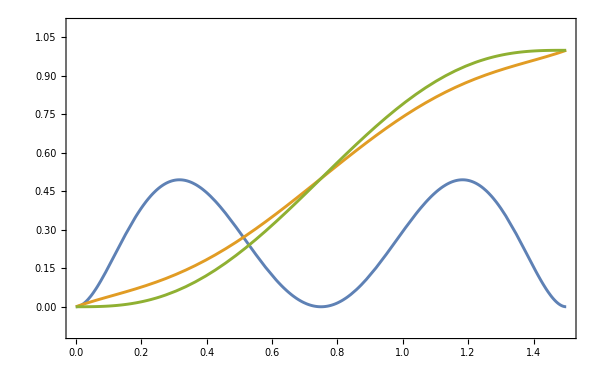

```mathematica
Table[Plot[{Evaluate[Simplify[1/4((d 433)/20)^2(D[fPol[t],{t,2}]/ω0^2)^2]/.solPol/.{d->1,ω0->2π}],Evaluate[Simplify[D[fPol[t],{t,2}]/ω0^2+fPol[t]]/.solPol/.{d->1,ω0->2π}],Evaluate[Simplify[fPol[t]]/.solPol/.{d->1,ω0->2π}]},{t,0,tf},PlotRange->{-0.1,1.1}],{tf,{1.5}}]
```

### Fourier components

```mathematica
fFourier[t_]:=d/tf t+Sum[β[n]Sin[(2π)/tf n t],{n,1,1}]
```

```mathematica
solFourier=Solve[{(*f[0]==0,f[tf]==d,*)(D[fFourier[t],t]/.t->0)==0(*,(D[f[t],t]/.t->tf)==0*)(*,(D[f[t],{t,2}]/.t->0)==0,(D[f[t],{t,2}]/.t->tf)==0*)},Table[β[n],{n,1}]]⟦1⟧;
fFourier[t]/.solFourier
```

(d t)/tf-(d Sin[(2 π t)/tf])/(2 π)

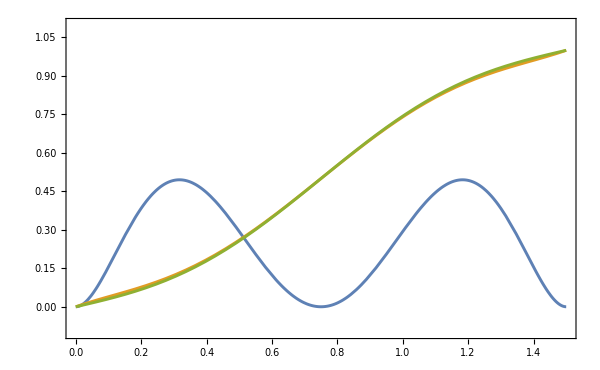

```mathematica
First[Table[Plot[{Evaluate[Simplify[1/4(433/20)^2(D[fPol[t],{t,2}]/ω0^2)^2]/.solPol/.{d->1,ω0->2π}],Evaluate[Simplify[D[fPol[t],{t,2}]/ω0^2+fPol[t]]/.solPol/.{d->1,ω0->2π}],Evaluate[Simplify[D[fFourier[t],{t,2}]/ω0^2+fFourier[t]]/.solFourier/.{d->1,ω0->2π}]},{t,0,1tf},PlotRange->{-0.1,1.1}],{tf,{1.5}}]]
```

### Polynomials – Catapult

```mathematica
fPol[t_]:=Sum[β[n] t^n,{n,1,5}]+β[0]
solPol=Solve[{fPol[0]==0,fPol[tf]==d,(D[fPol[t],t]/.t->0)==0,(D[fPol[t],t]/.t->tf)==v,(D[fPol[t],{t,2}]/.t->0)==0,(D[fPol[t],{t,2}]/.t->tf)==aMax},Table[β[n],{n,0,5}]]⟦1⟧;


speed=Solve[Simplify[D[(D[fPol[t],{t,2}]/ω0^2+fPol[t]),t]/.solPol/.t->tf]==v,v]⟦1⟧;
solPol=Simplify[solPol/.speed]


fPolExt[t_]:=β[0]+β[1]t+β[2] t^2;
solPolExt=Solve[{fPolExt[tf]==d,(D[fPolExt[t],t]/.t->tf)==(v/.speed),(D[fPolExt[t],{t,2}]/.t->tf)==aMax},Table[β[n],{n,0,2}]]⟦1⟧
```

{β[0]→0,β[1]→0,β[2]→0,β[3]→(20 d-3 aMax tf^2)/(6 tf^3),β[4]→(-40 d+9 aMax tf^2)/(12 tf^4),β[5]→d/tf^5-aMax/(4 tf^3)}

{β[0]→1/12 (-8 d+3 aMax tf^2),β[1]→-(-20 d+9 aMax tf^2)/(12 tf),β[2]→aMax/2}

0.0589635

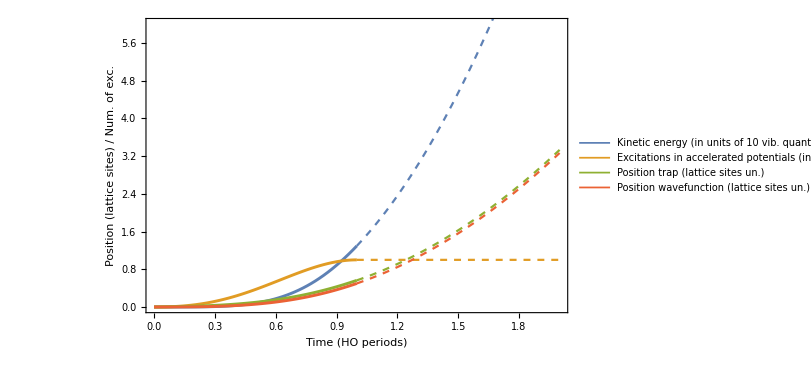

```mathematica
Module[{LatticeSite=433 √2 (* nanometer *),aHO=20 (* nanometer *)},
p=Flatten[Table[Table[{Simplify[1/(30  10^3 (* trap freq. *))(1000. (* size of the lattice in number of sites *))/((D[fPolExt[t],{t,2}]/ω0^2+fPolExt[t])/.solPolExt/.t->tf)],Show[{Plot[{Evaluate[Simplify[{(1/(4 ω0^2)(LatticeSite/aHO)^2 D[fPol[t],{t,1}]^2)/10,1/4(LatticeSite/aHO)^2(D[fPol[t],{t,2}]/ω0^2)^2,D[fPol[t],{t,2}]/ω0^2+fPol[t],fPol[t]}]/.solPol]},{t,0,tf},PlotLegends->{"Kinetic energy (in units of 10 vib. quanta)","Excitations in accelerated potentials (in units of vib. quanta)","Position trap (lattice sites un.)","Position wavefunction (lattice sites un.)"}],Plot[{Evaluate[Simplify[{(1/(4 ω0^2)(LatticeSite/aHO)^2 D[fPolExt[t],{t,1}]^2)/10,1/4(LatticeSite/aHO)^2(D[fPolExt[t],{t,2}]/ω0^2)^2,D[fPolExt[t],{t,2}]/ω0^2+fPolExt[t],fPolExt[t]}]/.solPolExt]},{t,tf,2tf},PlotStyle->Dashed]},FrameLabel->{"Time (HO periods)","Position (lattice sites) / Num. of exc."},PlotRange->{0,6}]},{aMax,{ (2 √NumEx aHO)/LatticeSite ω0^2}}],{d,{0.5}},{tf,{1}},{ω0,{2π}},{NumEx,{1}}],4]⟦1⟧;]

p⟦1⟧
p⟦2⟧
```

```mathematica
(*Export["~/Desktop/Catapult.pdf",p⟦2⟧]*)
```